# Discrete-time matching alleles coevolution with one-patch model

```mathematica
WH1[1,t_]:=pP[t](1-V) +(1-pP[t])S +(1-pP[t])(1-S)(1-V)
WH1[2,t_]:=(1-pP[t])(1-V)+pP[t]S +pP[t](1-S)(1-V) 
WP1[1,t_]:=pH[t]+(1-pH[t])(1-S)
WP1[2,t_]:=(1-pH[t])+pH[t](1-S)
```

```mathematica
pH2[t_]:=(pH[t] WH1[1,t])/(pH[t]WH1[1,t]+(1-pH[t])WH1[2,t])
pP2[t_]:=(pP[t] WP1[1,t])/(pP[t]WP1[1,t]+(1-pP[t])WP1[2,t])
```

```mathematica
pH2[t]/.pH[t]-> Subscript[p, H]/.pP[t]-> Subscript[p, P]//FullSimplify
```

(p_H (-1+V-S V+S V p_P))/(-1+V-S V p_P+S V p_H (-1+2 p_P))

```mathematica
pP2[t]/.pH[t]-> Subscript[p, H]/.pP[t]-> Subscript[p, P]//FullSimplify
```

((1-S+S p_H) p_P)/(1-S p_P+S p_H (-1+2 p_P))

### Numerical time series

```mathematica
inits1={i1-> 0.495,i2-> 0.5};
pars1={p1-> 0.4117647058823529,p2-> 0.2200911052505395};
pars2={p1-> 0.3939393939393939,p2-> 0.4368677407268642};
pars3={p1-> 0.37500000000000006,p2-> 0.9004329004329};
```

{p1→0.411765,p2→0.220091}

{p1→0.393939,p2→0.436868}

{p1→0.375,p2→0.900433}

```mathematica
Clear[timeSeries]
timeSeries[pars_,inits_,tmax_]:=timeSeries[pars,inits,tmax]=Block[
{WH1,WP1,pH1,pP1,pH2,pP2,S,V,mH,mP,pP,pH,i1,i2,i3,i4,p1,p2,p3,p4,out},

S=p1/.pars;
V=p2/.pars;

WH1[1,t_]:=pP[t](1-V) +(1-pP[t])S +(1-pP[t])(1-S)(1-V);
WH1[2,t_]:=(1-pP[t])(1-V)+pP[t]S +pP[t](1-S)(1-V) ;
WP1[1,t_]:=pH[t]+(1-pH[t])(1-S);
WP1[2,t_]:=(1-pH[t])+pH[t](1-S);

pH2[t_]:=(pH[t] WH1[1,t])/(pH[t]WH1[1,t]+(1-pH[t])WH1[2,t]);
pP2[t_]:=(pP[t] WP1[1,t])/(pP[t]WP1[1,t]+(1-pP[t])WP1[2,t]);

pH[t_]:=pH[t]=pH2[t-1];
pP[t_]:=pP[t]=pP2[t-1];

pH[0]=i1/.inits;
pP[0]=i2/.inits;

out={Table[j,{j,0,tmax}],
Table[pH[j],{j,0,tmax}],
Table[pP[j],{j,0,tmax}]}
]
```

```mathematica
maxT=1000;
```

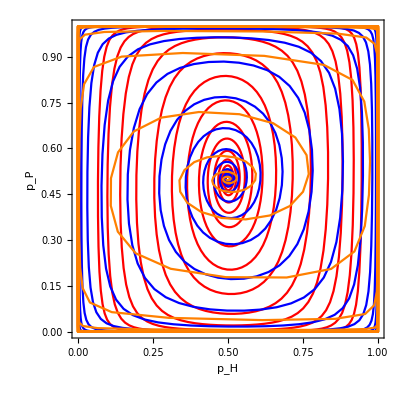

```mathematica
g=Show[ListLinePlot[Partition[Riffle[timeSeries[pars1,inits1,maxT][[2]],timeSeries[pars1,inits1,maxT][[3]]],2],PlotRange-> {{0,1},{0,1}},PlotStyle-> Red],
ListLinePlot[Partition[Riffle[timeSeries[pars2,inits1,maxT][[2]],timeSeries[pars2,inits1,maxT][[3]]],2],PlotRange-> {{0,1},{0,1}},PlotStyle-> Blue],ListLinePlot[Partition[Riffle[timeSeries[pars3,inits1,maxT][[2]],timeSeries[pars3,inits1,maxT][[3]]],2], PlotStyle-> Orange,PlotRange-> {{0,1},{0,1}}],Frame->  True,FrameLabel-> {"p_H","p_P"},AspectRatio-> 1]
```

```mathematica
Export["~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Phase.png",g,ImageResolution-> 300]
```

~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Phase.png

### Equilibria

```mathematica
equs={pH2[t],pP2[t]};
```

```mathematica
equi=Solve[equs=={pH[t],pP[t]},{pH[t],pP[t]}]
```

{{pH[t]→0,pP[t]→0},{pH[t]→1,pP[t]→0},{pH[t]→1/2,pP[t]→1/2},{pH[t]→0,pP[t]→1},{pH[t]→1,pP[t]→1}}

### Stability

```mathematica
JMtrx={
{D[pH2[t],pH[t]],D[pH2[t],pP[t]]},
{D[pP2[t],pH[t]],D[pP2[t],pP[t]]}};
```

```mathematica
Clear[JMtrxEqui,λList]
JMtrxEqui[e_]:=JMtrx/.equi[[e]]//Simplify;
λList[e_]:=JMtrxEqui[e]//Eigenvalues//FullSimplify;
```

#### Equilibrium 1 – both fixed for WT allele

```mathematica
JMtrxEqui[1]//MatrixForm
```

((-1+V-S V)/(-1+V) | 0
0 | 1-S)

```mathematica
λList[1]
```

{1-S,(-1+V-S V)/(-1+V)}

```mathematica
Map[Simplify[#,Assumptions->{1>S>0,0<V<1}]&,λList[1]]
```

{1-S,(-1+V-S V)/(-1+V)}

```mathematica
Map[Reduce[{#>1,1>S>0,0<V<1}]&,λList[1]]//MatrixForm
```

(False
0<V<1&&0<S<1)

With some degree of virulence and specificity, always unstable.

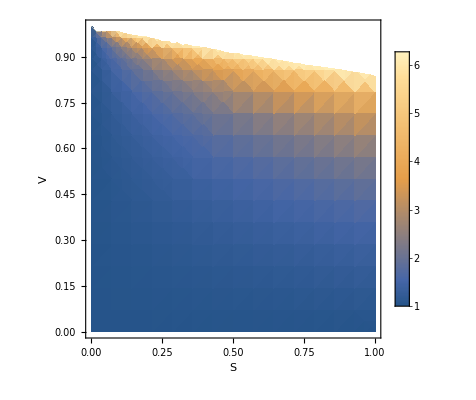

```mathematica
DensityPlot[(-1+V-S V)/(-1+V),{S,0,1},{V,0,1},FrameLabel-> {"S","V"},PlotLegends-> Automatic]
```

#### Equilibrium 2 – host fixed for mutant allele, parasite fixed for WT allele

```mathematica
equi[[2]]
```

{pH[t]→1,pP[t]→0}

```mathematica
JMtrxEqui[2]//MatrixForm
```

((1-V)/(1+(-1+S) V) | 0
0 | 1/(1-S))

```mathematica
λList[2]
```

{(1-V)/(1+(-1+S) V),1/(1-S)}

```mathematica
Map[Simplify[#,Assumptions->{1>S>0,0<V<1}]&,λList[2]]
```

{(1-V)/(1+(-1+S) V),1/(1-S)}

```mathematica
Map[Reduce[{#>1,1>S>0,0<V<1}]&,λList[2]]//MatrixForm
```

(False
0<V<1&&0<S<1)

With some degree of specificity, always unstable.

#### Equilibrium 3 – both polymorphic

```mathematica
equi[[3]]
```

{pH[t]→1/2,pP[t]→1/2}

```mathematica
JMtrxEqui[3]//MatrixForm
```

(1 | -(S V)/(2+(-2+S) V)
S/(2-S) | 1)

```mathematica
λList[3]
```

{(-4+4 V+S (2+(-4+S) V)-√((-2+S) S^2 V (2+(-2+S) V)))/((-2+S) (2+(-2+S) V)),(-4+4 V+S (2+(-4+S) V)+√((-2+S) S^2 V (2+(-2+S) V)))/((-2+S) (2+(-2+S) V))}

```mathematica
Map[Simplify[#,Assumptions->{1>S>0,0<V<1}]&,λList[3]]
```

{(-4+4 V+S (2+(-4+S) V)-S √((-2+S) V (2+(-2+S) V)))/((-2+S) (2+(-2+S) V)),(-4+4 V+S (2+(-4+S) V)+S √((-2+S) V (2+(-2+S) V)))/((-2+S) (2+(-2+S) V))}

```mathematica
re=Re[λList[3][[1]]/.{S-> 0.8,V-> 0.5}]
im=Im[λList[3][[1]]/.{S-> 0.8,V-> 0.5}]
Sqrt[re^2+im^2]
re=Re[λList[3][[1]]/.{S-> 0.6,V-> 0.5}]
im=Im[λList[3][[1]]/.{S-> 0.6,V-> 0.5}]
Sqrt[re^2+im^2]
```

1.

0.436436

1.09109

1.

0.314485

1.04828

Inconclusive?

```mathematica
(-4+4 V+S (2+(-4+S) V))/((-2+S) (2+(-2+S) V))//FullSimplify
```

1

#### Equilibrium 4 – host fixed for WT allele, parasite fixed for mutant allele

```mathematica
equi[[4]]
```

{pH[t]→0,pP[t]→1}

```mathematica
JMtrxEqui[4]//MatrixForm
```

((1-V)/(1+(-1+S) V) | 0
0 | 1/(1-S))

```mathematica
Map[Simplify[#,Assumptions->{1>S>0,0<V<1}]&,λList[4]]
```

{(1-V)/(1+(-1+S) V),1/(1-S)}

```mathematica
Map[Reduce[{#>1,1>S>0,0<V<1}]&,λList[4]]//MatrixForm
```

(False
0<V<1&&0<S<1)

With some degree of virulence and specificity, always unstable.

### Individual-Based Simulations

```mathematica
parsN={S-> 0,V->0.2,κH->300,κP->300,tMax->150};
parsN3={S-> 0,V->0.5,κH->300,κP->300,tMax->150};
pars1={S-> 0.8,V->0.2,a->0.1,κH->300,κP->300,tMax->150};
pars2={S->0.65,V->0.2,a->0.1,κH->300,κP->300,tMax->150};
pars3={S->0.8,V->0.5,a->0.1,κH->300,κP->300,tMax->150};
```

Absolute fitness values

```mathematica
WH[1,pVec_]:=pVec[[2]](1-V) +(1-pVec[[2]])S +(1-pVec[[2]])(1-S)(1-V);
WH[2,pVec_]:=(1-pVec[[2]])(1-V)+pVec[[2]]S +pVec[[2]](1-S)(1-V)  ;
WP[1,pVec_]:=pVec[[1]]+(1-pVec[[1]])(1-S);
WP[2,pVec_]:=(1-pVec[[1]])+pVec[[1]](1-S);
```

Relative fitness values

```mathematica
wH[pVec_]:=WH[1,pVec]/(pVec[[1]] WH[1,pVec]+(1-pVec[[1]])WH[2,pVec]) ;
wP[pVec_]:=WP[1,pVec]/(pVec[[2]] WP[1,pVec]+(1-pVec[[2]])WP[2,pVec]) ;
```

```mathematica
Clear[Sim]
Sim[pars_,intS_]:=Sim[pars,intS]=Block[{out,g,nHs,nPs,nHprime,nPprime},out={{1/2,1/2}}//N;
For[g=1,g≤(tMax/.pars),g++,

(*Selection*)
nHs=RandomVariate[BinomialDistribution[(κH/.pars),Min[Max[wH[out[[-1]]]out[[-1,1]]/.pars,0],1]]];
nPs=RandomVariate[BinomialDistribution[(κP/.pars),Min[Max[wP[out[[-1]]]out[[-1,2]]/.pars,0],1]]];

(*Number of type 1 hosts and parasites in next generation*)
nHprime=RandomVariate[BinomialDistribution[κH/.pars,Min[Max[nHs/(κH/.pars)//N,0],1]]];
nPprime=RandomVariate[BinomialDistribution[κP/.pars,Min[Max[nPs/(κP/.pars)//N,0],1]]];
AppendTo[out,{nHprime/κH,nPprime/κP}/.pars//N]
];
out
]
```

```mathematica
Clear[mean]
mean[pars_]:=mean[pars]=Mean[Table[2 Sim[pars,j][[;;,1]](1-Sim[pars,j][[;;,1]]),{j,1,2000}]]
```

```mathematica
Clear[SD]
SD[pars_]:=SD[pars]=Mean[Table[(2 Sim[pars,j][[;;,1]](1-Sim[pars,j][[;;,1]])-mean[pars])^2,{j,1,2000}]]//Sqrt;
```

```mathematica
leg2=LineLegend[{Directive[Blue,Opacity[0.2],Dashed],Directive[Blue,Opacity[0.4]],Directive[Blue]},{"Neutral","Coevolutionary, S=0.65","Coevolutionary, S=0.8"}]
```

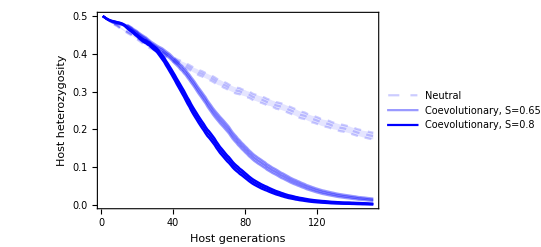

```mathematica
g1=Show[
ListLinePlot[{mean[parsN],mean[parsN]+(2SD[parsN])/Sqrt[2000],mean[parsN]-(2SD[parsN])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[2000],mean[pars2]-(2SD[pars2])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.4]],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
PlotRange-> {0,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False];
g1Legend=Legended[g1,leg2]
```

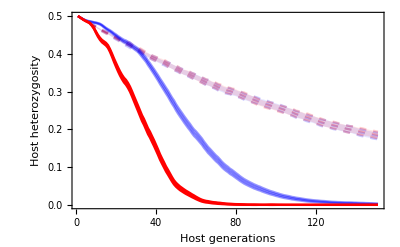

```mathematica
leg3=LineLegend[{Directive[Blue,Opacity[0.2],Dashed],Directive[Red,Opacity[0.2],Dashed],Directive[Blue],Directive[Red]},{"Neutral, V=0.2","Neutral, V=0.5","Coevolutionary, V=0.2","Coevolutionary, V=0.5"}]
g2=Show[
ListLinePlot[{mean[parsN],mean[parsN]+(2SD[parsN])/Sqrt[2000],mean[parsN]-(2SD[parsN])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[parsN3],mean[parsN3]+(2SD[parsN3])/Sqrt[2000],mean[parsN3]-(2SD[parsN3])/Sqrt[2000]},PlotStyle->Directive[Red,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.1]]}}}],

ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.4]],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[2000],mean[pars3]-(2SD[pars3])/Sqrt[2000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}},PlotRange-> All],
PlotRange-> All,Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False]
```

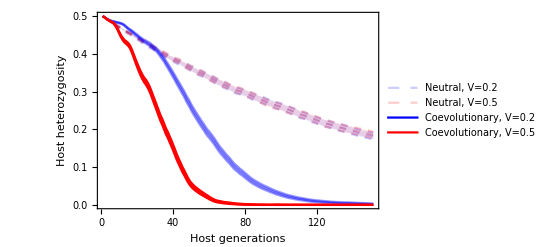

```mathematica
g2Legend=Legended[g2,leg3]
```

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Specificity.png",g1Legend,"PNG",ImageResolution-> 300]
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Virulence.png",g2Legend,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Specificity.png

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Virulence.png